# Computational Companion to “Generalized Quasi-Symmetric Nets: A Constructive Approach to the Equimodular Elliptic Type of m × n Kokotsakis Polyhedra” — Examples Helper

## A. Nurmatov, M. Skopenkov, F. Rist, J. Klein, D. L. Michels Tested on: Mathematica 14.0

## Section 1

## Results of Section 1 are used in Examples section

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[sA,sB,sC,sD,bA,bB,bC,bD,α,β,γ,δ,σ,rowS,gL,gLinv,chkR,statusChip,smallChip,colEight,colFour,colTest,eightRef,fourRef,eqName,resultsAll,pairs,kinds,prodId,quotId,prodIdInv,quotIdInv,convProd,convQuot,convQuotInv,posChk,sym,eqRatio1,eqRatio2,sqEq1,sqEq2,eqRow,eqRowS,eqFour,systemLines,bullet,idProd,idQuot,idProdInv,idQuotInv,idConvProd,idConvQuot,idConvQuotInv,posLine,tagOf,braceGrp,condBlock,ratioExpr,pairLbl];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colEight=RGBColor[0.90,0.55,0.05];
colFour=RGBColor[0.80,0.25,0.05];
colTest=RGBColor[0.10,0.35,0.75];
eightRef=Style["the eight equations",Bold,colEight];
fourRef=Style["the four equations",Bold,colFour];
eqName[s_String]:=Style[s,Bold,colFour];
bullet=Style["◼  ",12,colTest];
tagOf[glyph_,col_]:=Style[glyph,14,col];
pairLbl[l_,m_]:=Style[Row[{"pair (",l,", ",m,") :  "}],12,colEight];
braceGrp[items_List,sz_:13,col_:GrayLevel[0]]:=DisplayForm[RowBox[{GridBox[({ToBoxes[Style[#,sz,col]]}&/@items),GridBoxAlignment->{"Columns"->{{Left}}},GridBoxSpacings->{"Rows"->{{1.8}}}],StyleBox["}",FontColor->GrayLevel[0.55],SpanMaxSize->Infinity]}]];
(*The sines of the four numbers at the vertex i are the independent positive symbols sA[i],sB[i],sC[i],sD[i],those of the four barred numbers are bA[i],bB[i],bC[i],bD[i].Every identity below is a rational identity in these symbols,decided by Together;each passage from an equation between squares to the equation between the quantities is decided by Reduce over the positive reals.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
rowS[X_,i_]:=X[[3]][i] X[[4]][i]/(X[[1]][i] X[[2]][i]);
gL[X_,i_]:=X[[1]][i] X[[3]][i]/(X[[2]][i] X[[4]][i]);
gLinv[X_,i_]:=X[[2]][i] X[[4]][i]/(X[[1]][i] X[[3]][i]);
pairs={{2,3},{1,4}};
kinds={{sA,sB,sC,sD},{bA,bB,bC,bD}};
prodId[X_,i_]:=chkR[rowS[X,i] gL[X,i],(X[[3]][i]/X[[2]][i])^2];
quotId[X_,i_]:=chkR[rowS[X,i]/gL[X,i],(X[[4]][i]/X[[1]][i])^2];
prodIdInv[X_,i_]:=chkR[rowS[X,i] gLinv[X,i],(X[[4]][i]/X[[1]][i])^2];
quotIdInv[X_,i_]:=chkR[rowS[X,i]/gLinv[X,i],(X[[3]][i]/X[[2]][i])^2];
convProd[X_,i_]:=chkR[(X[[3]][i]/X[[2]][i]) (X[[4]][i]/X[[1]][i]),rowS[X,i]];
convQuot[X_,i_]:=chkR[(X[[3]][i]/X[[2]][i])/(X[[4]][i]/X[[1]][i]),gL[X,i]];
convQuotInv[X_,i_]:=chkR[(X[[4]][i]/X[[1]][i])/(X[[3]][i]/X[[2]][i]),gLinv[X,i]];
ratioExpr[X_,1,i_]:=X[[3]][i]/X[[2]][i];
ratioExpr[X_,2,i_]:=X[[4]][i]/X[[1]][i];
posChk[lhs_,rhs_]:=Module[{atoms,loc,rules,L,Rr},atoms=Union[Cases[{lhs,rhs},(sA|sB|sC|sD|bA|bB|bC|bD)[_],Infinity]];
loc=Table[Unique["w"],{Length[atoms]}];
rules=Thread[atoms->loc];
L=lhs/. rules;Rr=rhs/. rules;
Reduce[ForAll[Evaluate[loc],Evaluate[And@@(#>0&/@loc)],Evaluate[(L^2==Rr^2)⧦(L==Rr)]]]===True];
(*Display helpers.k=0:the numbers;k=1:the barred numbers.sw=True means the right-hand side has alpha<->beta,gamma<->delta interchanged.*)
sym[0,x_,j_]:=Subscript[x,j];
sym[1,x_,j_]:=OverBar[Subscript[x,j]];
eqRatio1[k_,l_,m_,sw_]:=With[{gl=sym[k,γ,l],bl=sym[k,β,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[Sin[gl]/Sin[bl]==Sin[dm]/Sin[am]],HoldForm[Sin[gl]/Sin[bl]==Sin[gm]/Sin[bm]]]];
eqRatio2[k_,l_,m_,sw_]:=With[{dl=sym[k,δ,l],al=sym[k,α,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[Sin[dl]/Sin[al]==Sin[gm]/Sin[bm]],HoldForm[Sin[dl]/Sin[al]==Sin[dm]/Sin[am]]]];
sqEq1[k_,l_,m_,sw_]:=With[{gl=sym[k,γ,l],bl=sym[k,β,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[(Sin[gl]/Sin[bl])^2==(Sin[dm]/Sin[am])^2],HoldForm[(Sin[gl]/Sin[bl])^2==(Sin[gm]/Sin[bm])^2]]];
sqEq2[k_,l_,m_,sw_]:=With[{dl=sym[k,δ,l],al=sym[k,α,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[(Sin[dl]/Sin[al])^2==(Sin[gm]/Sin[bm])^2],HoldForm[(Sin[dl]/Sin[al])^2==(Sin[dm]/Sin[am])^2]]];
(*eqRow:the equations of the pairs (1,2),(3,4);eqRowS:those of the pairs (2,3),(4,1);eqFour:equations (a)-(d) with generic indices l,m.*)
eqRow[k_,l_,m_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},HoldForm[Sin[al] Sin[dl]/(Sin[bl] Sin[gl])==Sin[am] Sin[dm]/(Sin[bm] Sin[gm])]];
eqRowS[k_,l_,m_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},HoldForm[Sin[gl] Sin[dl]/(Sin[al] Sin[bl])==Sin[gm] Sin[dm]/(Sin[am] Sin[bm])]];
eqFour[k_,inv_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},If[inv,HoldForm[Sin[al] Sin[gl]/(Sin[bl] Sin[dl])==Sin[bm] Sin[dm]/(Sin[am] Sin[gm])],HoldForm[Sin[al] Sin[gl]/(Sin[bl] Sin[dl])==Sin[am] Sin[gm]/(Sin[bm] Sin[dm])]]];
idProd[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])] HoldForm[Sin[a] Sin[g]/(Sin[b] Sin[d])]==(Sin[g]/Sin[b])^2]];
idQuot[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])]/HoldForm[Sin[a] Sin[g]/(Sin[b] Sin[d])]==(Sin[d]/Sin[a])^2]];
idProdInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])] HoldForm[Sin[b] Sin[d]/(Sin[a] Sin[g])]==(Sin[d]/Sin[a])^2]];
idQuotInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])]/HoldForm[Sin[b] Sin[d]/(Sin[a] Sin[g])]==(Sin[g]/Sin[b])^2]];
idConvProd[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g]/Sin[b]] HoldForm[Sin[d]/Sin[a]]==Sin[g] Sin[d]/(Sin[a] Sin[b])]];
idConvQuot[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g]/Sin[b]]/HoldForm[Sin[d]/Sin[a]]==Sin[a] Sin[g]/(Sin[b] Sin[d])]];
idConvQuotInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[d]/Sin[a]]/HoldForm[Sin[g]/Sin[b]]==Sin[b] Sin[d]/(Sin[a] Sin[g])]];
posLine[k_,l_,m_,which_,sw_]:=Row[{TraditionalForm[If[which==1,sqEq1[k,l,m,sw],sqEq2[k,l,m,sw]]],"   if and only if   ",TraditionalForm[If[which==1,eqRatio1[k,l,m,sw],eqRatio2[k,l,m,sw]]]}];
systemLines[swU_,swB_]:=Column[{Style[Row[{TraditionalForm[eqRatio1[0,2,3,swU]],",   ",TraditionalForm[eqRatio1[1,2,3,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio2[0,2,3,swU]],",   ",TraditionalForm[eqRatio2[1,2,3,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio1[0,1,4,swU]],",   ",TraditionalForm[eqRatio1[1,1,4,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio2[0,1,4,swU]],",   ",TraditionalForm[eqRatio2[1,1,4,swB]]}],13,colTest],Style[Row[{"together with the equations of the pairs (1, 2) and (3, 4) from ",eightRef," :"}],13,colTest],Style[Row[{TraditionalForm[eqRow[0,1,2]],",   ",TraditionalForm[eqRow[1,1,2]]}],13,colTest],Style[Row[{TraditionalForm[eqRow[0,3,4]],",   ",TraditionalForm[eqRow[1,3,4]]}],13,colTest]},Spacings->0.6];
(*condBlock renders and verifies the reduction for one condition;it returns {ok,column}.Glyphs:filled=identities used in the forward direction,hollow=identities used in the converse direction;circle=direct,triangle=inverted;brown=the numbers,magenta=the barred numbers.For an inverted kind,the left-hand side of the equation from the four equations is direct,so the direct identities are used at the indices 1,2 and the inverted ones at the indices 3,4.*)
condBlock[condName_,eqU_,eqB_,swU_,swB_]:=Module[{tagU=RGBColor[0.55,0.33,0.10],tagB=RGBColor[0.80,0.20,0.50],dot="●",tri="▲",odot="○",otri="△",eqUs=eqName[eqU],eqBs=eqName[eqB],sws={swU,swB},tags,idRows={},idOK={},convRows={},convOK={},posRows,okPos,ok,usedU,usedB},tags={tagU,tagB};
Do[With[{X=kinds[[ik]],kk=ik-1,sw=sws[[ik]],tg=tags[[ik]]},If[!sw,Module[{oP=And@@Table[prodId[X,j],{j,4}],oQ=And@@Table[quotId[X,j],{j,4}],oC=And@@Table[convProd[X,j]&&convQuot[X,j],{j,4}]},AppendTo[idOK,oP&&oQ];AppendTo[convOK,oC];
idRows=Join[idRows,{Style["For  i = 1, 2, 3, 4 :",13],Style[Row[{TraditionalForm[idProd[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oP]}],13],Style[Row[{TraditionalForm[idQuot[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oQ]}],13]}];
convRows=Join[convRows,{Style["For  i = 1, 2, 3, 4 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuot[kk]],"      ",tagOf[odot,tg],"   ",smallChip[oC]}],13]}]],Module[{oP=And@@Table[prodId[X,j],{j,2}],oQ=And@@Table[quotId[X,j],{j,2}],oPi=And@@Table[prodIdInv[X,j],{j,3,4}],oQi=And@@Table[quotIdInv[X,j],{j,3,4}],oC1=And@@Table[convProd[X,j]&&convQuot[X,j],{j,2}],oC2=And@@Table[convProd[X,j]&&convQuotInv[X,j],{j,3,4}]},AppendTo[idOK,oP&&oQ&&oPi&&oQi];
AppendTo[convOK,oC1&&oC2];
idRows=Join[idRows,{Style["For  i = 1, 2 :",13],Style[Row[{TraditionalForm[idProd[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oP]}],13],Style[Row[{TraditionalForm[idQuot[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oQ]}],13],Style["For  i = 3, 4 :",13],Style[Row[{TraditionalForm[idProdInv[kk]],"      ",tagOf[tri,tg],"   ",smallChip[oPi]}],13],Style[Row[{TraditionalForm[idQuotInv[kk]],"      ",tagOf[tri,tg],"   ",smallChip[oQi]}],13]}];
convRows=Join[convRows,{Style["For  i = 1, 2 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuot[kk]],"      ",tagOf[odot,tg],"   ",smallChip[oC1]}],13],Style["For  i = 3, 4 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuotInv[kk]],"      ",tagOf[otri,tg],"   ",smallChip[oC2]}],13]}]]]],{ik,2}];
posRows=Flatten[Table[With[{X=kinds[[ik]],sw=sws[[ik]]},Table[{posLine[ik-1,pr[[1]],pr[[2]],wh,sw],posChk[ratioExpr[X,wh,pr[[1]]],ratioExpr[X,If[sw,3-wh,wh],pr[[2]]]]},{pr,pairs},{wh,2}]],{ik,2}],2];
okPos=And@@posRows[[All,2]];
ok=(And@@idOK)&&(And@@convOK)&&okPos;
usedU=If[!swU,Row[{"Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from ",eightRef," by equation ",eqUs," from ",fourRef," for the pairs (2, 3) and (1, 4), and using the identities  ",tagOf[dot,tagU],"  at the four indices, we get"}],Row[{"Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from ",eightRef," by equation ",eqUs," from ",fourRef," for the pairs (2, 3) and (1, 4), and using the identities  ",tagOf[dot,tagU],"  at the indices 1, 2 and the identities  ",tagOf[tri,tagU],"  at the indices 3, 4, we get"}]];
usedB=If[!swB,Row[{"and, in the same way, with equation ",eqBs," from ",fourRef," and the identities  ",tagOf[dot,tagB],"  at the four indices,"}],Row[{"and, in the same way, with equation ",eqBs," from ",fourRef," and the identities  ",tagOf[dot,tagB],"  at the indices 1, 2 and  ",tagOf[tri,tagB],"  at the indices 3, 4,"}]];
{ok,Column[Join[{Style[Row[{"Condition ",condName," uses equations ",eqUs," and ",eqBs," from ",fourRef,"."}],13]},idRows,{Style[usedU,13],braceGrp[{TraditionalForm[sqEq1[0,2,3,swU]],TraditionalForm[sqEq2[0,2,3,swU]],TraditionalForm[sqEq1[0,1,4,swU]],TraditionalForm[sqEq2[0,1,4,swU]]},13],Style[usedB,13],braceGrp[{TraditionalForm[sqEq1[1,2,3,swB]],TraditionalForm[sqEq2[1,2,3,swB]],TraditionalForm[sqEq1[1,1,4,swB]],TraditionalForm[sqEq2[1,1,4,swB]]},13],Style["Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:",13],braceGrp[Table[Row[{posRows[[ir,1]],"   ",smallChip[posRows[[ir,2]]]}],{ir,Length[posRows]}],13],Style["Conversely:",13]},convRows,{Style[Row[{"so the product of the two ratio equations of a pair gives back the equation of that pair from ",eightRef,", and their quotient gives back equation ",eqUs,", respectively ",eqBs,", from ",fourRef,".  The equations of the pairs (1, 2) and (3, 4) from ",eightRef," are not touched."}],13]}],Spacings->0.8]}];
(* ============================================================*)(*PART 2:GIVEN PANEL*)(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style["For  i = 1, 2, 3, 4 :",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]]," ∈ (0, π),   ",TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]]}],13],Style[Row[{TraditionalForm[HoldForm[OverBar[Subscript[α,i]]==Subscript[σ,i]-Subscript[α,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]==Subscript[σ,i]-Subscript[β,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]==Subscript[σ,i]-Subscript[γ,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]==Subscript[σ,i]-Subscript[δ,i]]]," ∈ (0, π)"}],13],"",Style["Given equations:",Bold,14],Style[Row[{eightRef," , for the index pairs  (1, 2),  (2, 3),  (3, 4),  (4, 1) :"}],13],Row[{pairLbl[1,2],Style[Row[{TraditionalForm[eqRow[0,1,2]],",   ",TraditionalForm[eqRow[1,1,2]]}],13,colEight]}],Row[{pairLbl[2,3],Style[Row[{TraditionalForm[eqRowS[0,2,3]],",   ",TraditionalForm[eqRowS[1,2,3]]}],13,colEight]}],Row[{pairLbl[3,4],Style[Row[{TraditionalForm[eqRow[0,3,4]],",   ",TraditionalForm[eqRow[1,3,4]]}],13,colEight]}],Row[{pairLbl[4,1],Style[Row[{TraditionalForm[eqRowS[0,4,1]],",   ",TraditionalForm[eqRowS[1,4,1]]}],13,colEight]}],Style[Row[{"and ",fourRef," , for the index pairs  (",TraditionalForm[HoldForm[l]],", ",TraditionalForm[HoldForm[m]],") = (2, 3)  and  (1, 4) :"}],13],Style[Row[{eqName["(a)"],"  ",TraditionalForm[eqFour[0,False]],",     ",eqName["(b)"],"  ",TraditionalForm[eqFour[1,False]]}],13,colFour],Style[Row[{eqName["(c)"],"  ",TraditionalForm[eqFour[0,True]],",     ",eqName["(d)"],"  ",TraditionalForm[eqFour[1,True]]}],13,colFour],Style[Row[{"Condition (i) uses ",eqName["(a)"]," and ",eqName["(b)"],";  condition (ii) uses ",eqName["(c)"]," and ",eqName["(d)"],";  condition (iii) uses ",eqName["(a)"]," and ",eqName["(d)"],";  condition (iv) uses ",eqName["(b)"]," and ",eqName["(c)"],"."}],12,GrayLevel[0.35]],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims  ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style["Claim 1.  For condition (i), the twelve equations are equivalent to the system",Bold,13,colTest]}],systemLines[False,False],"",Row[{bullet,Style["Claim 2.  For condition (ii), the twelve equations are equivalent to the system",Bold,13,colTest]}],systemLines[True,True],Style["for condition (iii), to the system",Bold,13,colTest],systemLines[False,True],Style["and for condition (iv), to the system",Bold,13,colTest],systemLines[True,False],Style[Row[{"that is, to the system of Claim 1 with  ",TraditionalForm[HoldForm[Subscript[α,i]]]," ↔ ",TraditionalForm[HoldForm[Subscript[β,i]]],",  ",TraditionalForm[HoldForm[Subscript[γ,i]]]," ↔ ",TraditionalForm[HoldForm[Subscript[δ,i]]],"  substituted in the right-hand sides, for  i ∈ {3, 4} :  in the first and in the second column of the ratio equations for (ii), in the second column only for (iii), in the first column only for (iv)."}],12,GrayLevel[0.35]]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];
(* ============================================================*)(*PART 3:CLAIM 1*)(* ============================================================*)
resultsAll={};
Module[{col=RGBColor[0.10,0.30,0.70],blk},blk=condBlock["(i)","(a)","(b)",False,False];
AppendTo[resultsAll,blk[[1]]];
Print[Panel[Column[{Row[{Style["Claim 1:  condition (i)",Bold,15,col],Spacer[20],statusChip[blk[[1]]]}],Style["Verification:",Bold,13],blk[[2]],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 4:CLAIM 2*)(* ============================================================*)
Module[{col=RGBColor[0.55,0.25,0.70],blk2,blk3,blk4,ok},blk2=condBlock["(ii)","(c)","(d)",True,True];
blk3=condBlock["(iii)","(a)","(d)",False,True];
blk4=condBlock["(iv)","(b)","(c)",True,False];
ok=blk2[[1]]&&blk3[[1]]&&blk4[[1]];
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Claim 2:  conditions (ii), (iii), (iv)",Bold,15,col],Spacer[20],statusChip[ok]}],Style[Row[{"Equations ",eqName["(c)"]," and ",eqName["(d)"]," from ",fourRef," are equations ",eqName["(a)"]," and ",eqName["(b)"]," with inverted right-hand sides; their left-hand sides, at the indices 1 and 2, are those of ",eqName["(a)"]," and ",eqName["(b)"],"."}],13],Style["Verification for condition (ii):",Bold,13],Row[{blk2[[2]],Spacer[20],statusChip[blk2[[1]]]}],"",Style["Verification for condition (iii):",Bold,13],Row[{blk3[[2]],Spacer[20],statusChip[blk3[[1]]]}],"",Style["Verification for condition (iv):",Bold,13],Row[{blk4[[2]],Spacer[20],statusChip[blk4[[1]]]}],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 5:SUMMARY*)(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
For  i = 1, 2, 3, 4 :
α_i, β_i, γ_i, δ_i ∈ (0, π),   σ_i==1/2 (α_i+β_i+γ_i+δ_i)
OverBar[α_i]==σ_i-α_i,   OverBar[β_i]==σ_i-β_i,   OverBar[γ_i]==σ_i-γ_i,   OverBar[δ_i]==σ_i-δ_i ∈ (0, π)

Given equations:
the eight equations , for the index pairs  (1, 2),  (2, 3),  (3, 4),  (4, 1) :
pair (1, 2) :  (sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
pair (2, 3) :  (sin(γ_2) sin(δ_2))/(sin(α_2) sin(β_2))==(sin(γ_3) sin(δ_3))/(sin(α_3) sin(β_3)),   (sin(OverBar[γ_2]) sin(OverBar[δ_2]))/(sin(OverBar[α_2]) sin(OverBar[β_2]))==(sin(OverBar[γ_3]) sin(OverBar[δ_3]))/(sin(OverBar[α_3]) sin(OverBar[β_3]))
pair (3, 4) :  (sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
pair (4, 1) :  (sin(γ_4) sin(δ_4))/(sin(α_4) sin(β_4))==(sin(γ_1) sin(δ_1))/(sin(α_1) sin(β_1)),   (sin(OverBar[γ_4]) sin(OverBar[δ_4]))/(sin(OverBar[α_4]) sin(OverBar[β_4]))==(sin(OverBar[γ_1]) sin(OverBar[δ_1]))/(sin(OverBar[α_1]) sin(OverBar[β_1]))
and the four equations , for the index pairs  (l, m) = (2, 3)  and  (1, 4) :
(a)  (sin(α_l) sin(γ_l))/(sin(β_l) sin(δ_l))==(sin(α_m) sin(γ_m))/(sin(β_m) sin(δ_m)),     (b)  (sin(OverBar[α_l]) sin(OverBar[γ_l]))/(sin(OverBar[β_l]) sin(OverBar[δ_l]))==(sin(OverBar[α_m]) sin(OverBar[γ_m]))/(sin(OverBar[β_m]) sin(OverBar[δ_m]))
(c)  (sin(α_l) sin(γ_l))/(sin(β_l) sin(δ_l))==(sin(β_m) sin(δ_m))/(sin(α_m) sin(γ_m)),     (d)  (sin(OverBar[α_l]) sin(OverBar[γ_l]))/(sin(OverBar[β_l]) sin(OverBar[δ_l]))==(sin(OverBar[β_m]) sin(OverBar[δ_m]))/(sin(OverBar[α_m]) sin(OverBar[γ_m]))
Condition (i) uses (a) and (b);  condition (ii) uses (c) and (d);  condition (iii) uses (a) and (d);  condition (iv) uses (b) and (c).
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ :
◼  Claim 1.  For condition (i), the twelve equations are equivalent to the system
(sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
(sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))

◼  Claim 2.  For condition (ii), the twelve equations are equivalent to the system
(sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
(sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
for condition (iii), to the system
(sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
(sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
and for condition (iv), to the system
(sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
(sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
that is, to the system of Claim 1 with  α_i ↔ β_i,  γ_i ↔ δ_i  substituted in the right-hand sides, for  i ∈ {3, 4} :  in the first and in the second column of the ratio equations for (ii), in the second column only for (iii), in the first column only for (iv).

Claim 1:  condition (i)Verified
Verification:
Condition (i) uses equations (a) and (b) from the four equations.
For  i = 1, 2, 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (a) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the four indices, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2}
and, in the same way, with equation (b) from the four equations and the identities  ●  at the four indices,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑}
Conversely:
For  i = 1, 2, 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (a), respectively (b), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.
Together, these give Claim 1.

Claim 2:  conditions (ii), (iii), (iv)Verified
Equations (c) and (d) from the four equations are equations (a) and (b) with inverted right-hand sides; their left-hand sides, at the indices 1 and 2, are those of (a) and (b).
Verification for condition (ii):
Condition (ii) uses equations (c) and (d) from the four equations.
For  i = 1, 2 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))==((sin(δ_i))/(sin(α_i)))^2      ▲   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i)))==((sin(γ_i))/(sin(β_i)))^2      ▲   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ▲   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i])))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ▲   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (c) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the indices 1, 2 and the identities  ▲  at the indices 3, 4, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2}
and, in the same way, with equation (d) from the four equations and the identities  ●  at the indices 1, 2 and  ▲  at the indices 3, 4,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑}
Conversely:
For  i = 1, 2 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(δ_i))/(sin(α_i)))/((sin(γ_i))/(sin(β_i)))==(sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))      △   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))/((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))==(sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))      △   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (c), respectively (d), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified

Verification for condition (iii):
Condition (iii) uses equations (a) and (d) from the four equations.
For  i = 1, 2, 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ▲   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i])))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ▲   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (a) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the four indices, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2}
and, in the same way, with equation (d) from the four equations and the identities  ●  at the indices 1, 2 and  ▲  at the indices 3, 4,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑}
Conversely:
For  i = 1, 2, 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))/((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))==(sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))      △   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (a), respectively (d), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified

Verification for condition (iv):
Condition (iv) uses equations (b) and (c) from the four equations.
For  i = 1, 2 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))==((sin(δ_i))/(sin(α_i)))^2      ▲   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i)))==((sin(γ_i))/(sin(β_i)))^2      ▲   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (b) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the indices 1, 2 and the identities  ▲  at the indices 3, 4, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2}
and, in the same way, with equation (c) from the four equations and the identities  ●  at the four indices,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑}
Conversely:
For  i = 1, 2 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(δ_i))/(sin(α_i)))/((sin(γ_i))/(sin(β_i)))==(sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))      △   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (b), respectively (c), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified
Together, these give Claim 2.

ALL CLAIMS VERIFIED

## Section 2

## Results of Section 2 are used in the proof of Lemma 16

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,σ,X,sigOf,barsOf,statusChip,smallChip,colTest,bullet,cases,caseCol,vertsOf,unk,relsOf,relDisp,ratZeroQ,zeroListQ,sgnCombos,combOf,congrQ,complQ,aOf,bOf,cOf,dOf,MOf,rOf,sOf,fOf,resultsAll,barSym,barTargets,barTargetDisp,quadDisp,solveCase,n1Disp];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colTest=RGBColor[0.10,0.35,0.75];
bullet=Style["◼  ",12,colTest];
(*The numbers at the vertex 1 are the independent symbols alpha,beta,gamma,delta;the numbers at the vertices 2,3,4 are the unique solution of the relations of each case,found by Solve.Every check below is a linear or a trigonometric identity in alpha,beta,gamma,delta;a trigonometric identity is decided on the numerator of the difference of its two sides,by TrigReduce or TrigExpand followed by Simplify.*)
X={α,β,γ,δ};
sigOf[{a_,b_,c_,d_}]:=(a+b+c+d)/2;
barsOf[Y_List]:=sigOf[Y]-Y;
ratZeroQ[expr_]:=Module[{n=Numerator[Together[expr]]},Simplify[TrigReduce[n]]===0||Simplify[TrigExpand[n]]===0];
zeroListQ[lst_List]:=And@@(Simplify[#]===0&/@lst);
sgnCombos=Tuples[{1,-1},3];
combOf[Y_List,s_List]:=Y[[1]]+s[[1]] Y[[2]]+s[[2]] Y[[3]]+s[[3]] Y[[4]];
congrQ[Yv_List,Y1_List]:=And@@Table[Or@@Flatten[Table[IntegerQ[Simplify[(combOf[Yv,s]-e combOf[Y1,sp])/(2 π)]],{sp,sgnCombos},{e,{1,-1}}]],{s,sgnCombos}];
complQ[Yv_List,ref_List]:=And@@(MemberQ[Join[ref,π-ref],Simplify[#]]&/@Yv);
aOf[Y_List]:=Sin[Y[[1]]]/Sin[barsOf[Y][[1]]];
bOf[Y_List]:=Sin[Y[[2]]]/Sin[barsOf[Y][[2]]];
cOf[Y_List]:=Sin[Y[[3]]]/Sin[barsOf[Y][[3]]];
dOf[Y_List]:=Sin[Y[[4]]]/Sin[barsOf[Y][[4]]];
MOf[Y_List]:=aOf[Y] bOf[Y] cOf[Y] dOf[Y];
rOf[Y_List]:=aOf[Y] dOf[Y];
sOf[Y_List]:=cOf[Y] dOf[Y];
fOf[Y_List]:=aOf[Y] cOf[Y];
cases={"(a)","(b)","(c)","(d)"};
caseCol["(a)"]=RGBColor[0.55,0.33,0.10];
caseCol["(b)"]=RGBColor[0.00,0.45,0.25];
caseCol["(c)"]=RGBColor[0.10,0.45,0.65];
caseCol["(d)"]=RGBColor[0.55,0.15,0.25];
unk={{a2,b2,g2,d2},{a3,b3,g3,d3},{a4,b4,g4,d4}};
relsOf["(a)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[3]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[4]]),b[[1]]-b[[3]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[4]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(b)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[4]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[3]]),d[[1]]-g[[4]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[3]])}];
relsOf["(c)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[3]]),b[[1]]-b[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[3]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(d)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[4]]),d[[1]]-g[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[4]])}];
solveCase[c_]:=Module[{sol=Solve[Thread[relsOf[c][Prepend[unk,X]]==0],Flatten[unk]]},If[Length[sol]==1,Prepend[unk/. sol[[1]],X],Missing[]]];
Do[vertsOf[c]=solveCase[c],{c,cases}];
relDisp["(a)"]={HoldForm[Subscript[α,1]==Subscript[α,3]==π-Subscript[α,2]==π-Subscript[α,4]],HoldForm[Subscript[β,1]==Subscript[β,3]==π-Subscript[β,2]==π-Subscript[β,4]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(b)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,4]==π-Subscript[γ,2]==π-Subscript[δ,3]],HoldForm[Subscript[δ,1]==Subscript[γ,4]==π-Subscript[δ,2]==π-Subscript[γ,3]]};
relDisp["(c)"]={HoldForm[Subscript[α,1]==Subscript[α,4]==π-Subscript[α,2]==π-Subscript[α,3]],HoldForm[Subscript[β,1]==Subscript[β,4]==π-Subscript[β,2]==π-Subscript[β,3]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(d)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,3]==π-Subscript[γ,2]==π-Subscript[δ,4]],HoldForm[Subscript[δ,1]==Subscript[γ,3]==π-Subscript[δ,2]==π-Subscript[γ,4]]};
(*Display helpers.*)
quadDisp[k_]:=HoldForm[{Subscript[α,k],Subscript[β,k],Subscript[γ,k],Subscript[δ,k]}];
n1Disp[k_]:=Row[{TraditionalForm[HoldForm[Subscript[α,k]±Subscript[β,k]±Subscript[γ,k]±Subscript[δ,k]]]," ≠ 0  (mod 2π)  for all choices of the signs ±"}];
barSym=OverBar[Subscript[#,1]]&/@{α,β,γ,δ};
barTargets["(a)"][B_]:={π-B,B,π-B};
barTargets["(b)"][B_]:={π-B,π-B[[{2,1,4,3}]],B[[{2,1,4,3}]]};
barTargets["(c)"][B_]:={π-B,{B[[2]],B[[1]],π-B[[4]],π-B[[3]]},{π-B[[2]],π-B[[1]],B[[4]],B[[3]]}};
barTargets["(d)"][B_]:={π-B,{B[[1]],B[[2]],π-B[[3]],π-B[[4]]},{π-B[[1]],π-B[[2]],B[[3]],B[[4]]}};
barTargetDisp[c_,k_]:=TraditionalForm[HoldForm[{OverBar[Subscript[α,k]],OverBar[Subscript[β,k]],OverBar[Subscript[γ,k]],OverBar[Subscript[δ,k]]}]==barTargets[c][barSym][[k-1]]];
resultsAll={};
(* ============================================================*)(*PART 2:GIVEN PANEL*)(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{TraditionalForm[quadDisp[1]]," = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π),    ",n1Disp[1]}],13],Style[Row[{TraditionalForm[HoldForm[OverBar[Subscript[α,1]]==Subscript[σ,1]-α]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[β,1]]==Subscript[σ,1]-β]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,1]]==Subscript[σ,1]-γ]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,1]]==Subscript[σ,1]-δ]]," ∈ (0, π),   where  ",TraditionalForm[HoldForm[Subscript[σ,1]==(α+β+γ+δ)/2]]}],13],"",Style["Definitions, for  i = 1, 2, 3, 4 :",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[α,i]]==Subscript[σ,i]-Subscript[α,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]==Subscript[σ,i]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]==Subscript[σ,i]-Subscript[γ,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]==Subscript[σ,i]-Subscript[δ,i]]],",   ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[a,i]==Sin[Subscript[α,i]]/Sin[OverBar[Subscript[α,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[b,i]==Sin[Subscript[β,i]]/Sin[OverBar[Subscript[β,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[c,i]==Sin[Subscript[γ,i]]/Sin[OverBar[Subscript[γ,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[d,i]==Sin[Subscript[δ,i]]/Sin[OverBar[Subscript[δ,i]]]]],",   ",TraditionalForm[HoldForm[Subscript[M,i]==Subscript[a,i] Subscript[b,i] Subscript[c,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[r,i]==Subscript[a,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[s,i]==Subscript[c,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[f,i]==Subscript[a,i] Subscript[c,i]]],",   ",TraditionalForm[HoldForm[Subscript[z,i]==1/(Subscript[f,i]-1)]],",   ",TraditionalForm[HoldForm[χ==Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4] Sign[Subscript[z,1] Subscript[z,3]]]]}],13],"",Style["Given cases:",Bold,14],Sequence@@Table[Style[Row[{Style["Case "<>c<>"   ",Bold,13],Row[Riffle[TraditionalForm/@relDisp[c],",    "]]}],13,caseCol[c]],{c,cases}],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims  ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style[Row[{"Claim 1.  In each case, the relations determine  ",TraditionalForm[quadDisp[2]],", ",TraditionalForm[quadDisp[3]],", ",TraditionalForm[quadDisp[4]],"  uniquely,   ",TraditionalForm[HoldForm[Subscript[δ,1]+Subscript[δ,2]+Subscript[δ,3]+Subscript[δ,4]==2 π]],",   and  ",n1Disp[i],"  for  i = 2, 3, 4."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 2.  In each case,  ",TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[α,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]]]," ∈ (0, π)  and  ",TraditionalForm[HoldForm[Subscript[M,i]>0]],"  for each  i = 1, 2, 3, 4."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 3.  In each case, for each  i = 1, 2, 3, 4 :  ",TraditionalForm[HoldForm[Subscript[σ,i]∉π ℤ]],",  ",TraditionalForm[HoldForm[Subscript[f,i]!=1]],",  ",TraditionalForm[HoldForm[Subscript[M,i]!=1]],";  hence  ",TraditionalForm[HoldForm[Subscript[ε,i]∈{±1}]],",  ",TraditionalForm[HoldForm[Subscript[z,i]]],"  is well defined, and  ",TraditionalForm[HoldForm[χ∈{±1}]],"."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 4.  In each case,  ",TraditionalForm[HoldForm[Subscript[M,1]==Subscript[M,2]==Subscript[M,3]==Subscript[M,4]]]," =: M   and   ",TraditionalForm[HoldForm[Subscript[r,1]==Subscript[r,2]]],",  ",TraditionalForm[HoldForm[Subscript[s,1]==Subscript[s,4]]],",  ",TraditionalForm[HoldForm[Subscript[r,3]==Subscript[r,4]]],",  ",TraditionalForm[HoldForm[Subscript[s,2]==Subscript[s,3]]],"."}],Bold,13,colTest]}],"",Row[{bullet,Style["Claim 5.  With  M  as in Claim 4:",Bold,13,colTest]}],Style[Row[{"        in case (a),   ",TraditionalForm[HoldForm[Subscript[f,2]==Subscript[f,3]]],",  ",TraditionalForm[HoldForm[Subscript[f,1]==Subscript[f,4]]],",  ",TraditionalForm[HoldForm[χ (Subscript[f,2]-1) (Subscript[f,1]-1)>0]],";"}],Bold,13,colTest],Style[Row[{"        in case (b),   ",TraditionalForm[HoldForm[Subscript[f,2] Subscript[f,3]==Subscript[f,1] Subscript[f,4]==M]],";"}],Bold,13,colTest],Style[Row[{"        in case (c),   ",TraditionalForm[HoldForm[Subscript[f,2]+Subscript[f,3]-Subscript[f,2] Subscript[f,3]==Subscript[f,1]+Subscript[f,4]-Subscript[f,1] Subscript[f,4]==M]],",  ",TraditionalForm[HoldForm[χ (1-M)>0]],";"}],Bold,13,colTest],Style[Row[{"        in case (d),   ",TraditionalForm[HoldForm[(Subscript[f,2]+Subscript[f,3]-1)/(Subscript[f,2] Subscript[f,3])==(Subscript[f,1]+Subscript[f,4]-1)/(Subscript[f,1] Subscript[f,4])==1/M]],"."}],Bold,13,colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];
(* ============================================================*)(*PART 3:CLAIM 1*)(* ============================================================*)
ClearAll[congrOneQ,comboDisp,sgnStr];
(*congrOneQ:the number differs from plus or minus one of alpha+-beta+-gamma+-delta by an integer multiple of 2 pi.*)
congrOneQ[expr_,Y1_List]:=Or@@Flatten[Table[IntegerQ[Simplify[(expr-e combOf[Y1,sp])/(2 π)]],{sp,sgnCombos},{e,{1,-1}}]];
sgnStr[1]=" + ";sgnStr[-1]=" − ";
comboDisp[k_,s_List]:=Row[{TraditionalForm[HoldForm[Subscript[α,k]]],sgnStr[s[[1]]],TraditionalForm[HoldForm[Subscript[β,k]]],sgnStr[s[[2]]],TraditionalForm[HoldForm[Subscript[γ,k]]],sgnStr[s[[3]]],TraditionalForm[HoldForm[Subscript[δ,k]]]}];
Module[{col=RGBColor[0.10,0.30,0.70],rows={},ok=True},Do[Module[{V=vertsOf[c],okUnique,rsym,rsol,okV,okSum,okN1,signRows},okUnique=!MissingQ[V];
If[okUnique,rsym=relsOf[c][Prepend[unk,X]];rsol=relsOf[c][V];
okV=Table[zeroListQ[rsol[[Flatten[Position[rsym,_?(!FreeQ[#,Alternatives@@unk[[k-1]]]&),{1},Heads->False]]]]],{k,2,4}];
okSum=Simplify[Total[V[[All,4]]]-2 π]===0;
okN1=Table[congrOneQ[combOf[V[[k]],s],V[[1]]],{k,2,4},{s,sgnCombos}],okV={False,False,False};okSum=False;
okN1=Table[False,{3},{8}]];
ok=ok&&okUnique&&(And@@okV)&&okSum&&(And@@Flatten[okN1]);
signRows=If[okUnique,Table[Column[Prepend[Table[Row[{comboDisp[k,s]," = ",TraditionalForm[Simplify[combOf[V[[k]],s]]],"   ",smallChip[okN1[[k-1,is]]]}],{is,8},{s,{sgnCombos[[is]]}}][[All,1]],Style[Row[{"i = ",k," :"}],13]],Spacings->0.4],{k,2,4}],{}];
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :   ",Bold,13,caseCol[c]],"the relations   ",Row[Riffle[TraditionalForm/@relDisp[c],",   "]],"   have the unique solution"}],13],If[okUnique,Column[{Style[Row[{TraditionalForm[quadDisp[2]==V[[2]]],"   ",smallChip[okV[[1]]]}],13],Style[Row[{TraditionalForm[quadDisp[3]==V[[3]]],"   ",smallChip[okV[[2]]]}],13],Style[Row[{TraditionalForm[quadDisp[4]==V[[4]]],"   ",smallChip[okV[[3]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[δ,1]+Subscript[δ,2]+Subscript[δ,3]+Subscript[δ,4]==2 π]],"   ",smallChip[okSum]}],13]},Spacings->0.4],Style[Row[{"(no unique solution)   ",smallChip[False]}],13]],Style["for  i = 2, 3, 4  and all choices of the signs:",13],Sequence@@(Style[#,13]&/@signRows),Style[Row[{"each value differs from  ",TraditionalForm[HoldForm[±(α±β±γ±δ)]],"  by an integer multiple of 2π, and  ",n1Disp[1],"  by the hypothesis;  hence  ",n1Disp[i],"  for  i = 2, 3, 4."}],13],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 1:  the four cases",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:",Bold,13]},Most[rows],{Style["Together, these give Claim 1.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 4:CLAIM 2*)(* ============================================================*)
Module[{col=RGBColor[0.55,0.25,0.70],B=barsOf[X],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],okCompl,oks},okCompl=Table[complQ[V[[k]],X],{k,2,4}];
oks=Table[zeroListQ[barsOf[V[[k]]]-barTargets[c][B][[k-1]]],{k,2,4}];
ok=ok&&(And@@okCompl)&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Join[Table[Style[Row[{ind,TraditionalForm[quadDisp[k]==V[[k]]]," ,  each entry is one of  α, β, γ, δ  or its complement to π   ",smallChip[okCompl[[k-1]]]}],13],{k,2,4}],Table[Style[Row[{ind,barTargetDisp[c,k],"   ",smallChip[oks[[k-1]]]}],13],{k,2,4}]],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 2:  the numbers and the barred numbers at the vertices 2, 3, 4",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  substituting the quadruples of Claim 1 into the definitions of the half sums and of the barred numbers, we get",Bold,13]},Most[rows],{Style[Row[{"Since  α, β, γ, δ  and  ",TraditionalForm[HoldForm[OverBar[Subscript[α,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[β,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[γ,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[δ,1]]]],"  lie in  (0, π)  by the hypotheses, it follows that their complements to π lie in  (0, π)  as well;  hence all numbers and barred numbers at the vertices 2, 3, 4 lie in  (0, π),  all sines in the definitions of  ",TraditionalForm[HoldForm[Subscript[a,i]]],", ",TraditionalForm[HoldForm[Subscript[b,i]]],", ",TraditionalForm[HoldForm[Subscript[c,i]]],", ",TraditionalForm[HoldForm[Subscript[d,i]]],"  are positive, and  ",TraditionalForm[HoldForm[Subscript[M,i]>0]],"  for each  i = 1, 2, 3, 4.  Together, these give Claim 2."}],13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 5:CLAIM 3*)(* ============================================================*)
Module[{col=RGBColor[0.00,0.50,0.50],B=barsOf[X],sg=sigOf[X],okS,okA,okG,okD,okF,okM,ok,ind="        "},okS=Simplify[2 sg-(α+β+γ+δ)]===0;
okA=Simplify[2 (B[[1]]-β)-(-α-β+γ+δ)]===0;
okG=Simplify[2 (B[[3]]-β)-(α-β-γ+δ)]===0;
okD=Simplify[2 (B[[4]]-β)-(α-β+γ-δ)]===0;
okF=ratZeroQ[fOf[X]-1-Sin[sg] Sin[B[[4]]-β]/(Sin[B[[1]]] Sin[B[[3]]])];
okM=ratZeroQ[1-MOf[X]-Sin[sg] Sin[B[[1]]-β] Sin[B[[3]]-β] Sin[B[[4]]-β]/(Sin[B[[1]]] Sin[B[[2]]] Sin[B[[3]]] Sin[B[[4]]])];
ok=okS&&okA&&okG&&okD&&okF&&okM;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Claim 3:  the half sums, the quantities  \!\(\*SubscriptBox[\(f\), \(i\)]\)  and  \!\(\*SubscriptBox[\(M\), \(i\)]\)",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  the following identities hold for an arbitrary quadruple, hence at each vertex  i = 1, 2, 3, 4 :",Bold,13],Column[{Style[Row[{ind,TraditionalForm[HoldForm[2 Subscript[σ,i]==Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okS]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[α,i]]-Subscript[β,i])==-Subscript[α,i]-Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okA]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[γ,i]]-Subscript[β,i])==Subscript[α,i]-Subscript[β,i]-Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okG]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[δ,i]]-Subscript[β,i])==Subscript[α,i]-Subscript[β,i]+Subscript[γ,i]-Subscript[δ,i]]],"   ",smallChip[okD]}],13],Style[Row[{ind,TraditionalForm[HoldForm[Subscript[f,i]-1==Sin[Subscript[σ,i]] Sin[OverBar[Subscript[δ,i]]-Subscript[β,i]]/(Sin[OverBar[Subscript[α,i]]] Sin[OverBar[Subscript[γ,i]]])]],"   ",smallChip[okF]}],13],Style[Row[{ind,TraditionalForm[HoldForm[1-Subscript[M,i]==Sin[Subscript[σ,i]] Sin[OverBar[Subscript[α,i]]-Subscript[β,i]] Sin[OverBar[Subscript[γ,i]]-Subscript[β,i]] Sin[OverBar[Subscript[δ,i]]-Subscript[β,i]]/(Sin[OverBar[Subscript[α,i]]] Sin[OverBar[Subscript[β,i]]] Sin[OverBar[Subscript[γ,i]]] Sin[OverBar[Subscript[δ,i]]])]],"   ",smallChip[okM]}],13]},Spacings->0.4],Style[Row[{"The right-hand sides of the first four identities are, up to sign, numbers  ",TraditionalForm[HoldForm[Subscript[α,i]±Subscript[β,i]±Subscript[γ,i]±Subscript[δ,i]]]," ,  which are  ≠ 0  (mod 2π)  by the hypothesis and Claim 1;  hence  ",TraditionalForm[HoldForm[Subscript[σ,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[α,i]]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]-Subscript[β,i]]],"  are not in  πℤ,  and their sines are nonzero.  Since the sines of the barred numbers are nonzero by Claim 2, it follows from the last two identities that  ",TraditionalForm[HoldForm[Subscript[f,i]!=1]],"  and  ",TraditionalForm[HoldForm[Subscript[M,i]!=1]]," .  Hence  ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]∈{±1}]],",  ",TraditionalForm[HoldForm[Subscript[z,i]==1/(Subscript[f,i]-1)]],"  is well defined and nonzero, and  ",TraditionalForm[HoldForm[χ∈{±1}]]," .  Together, these give Claim 3."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 6:CLAIM 4*)(* ============================================================*)
Module[{col=RGBColor[0.75,0.35,0.05],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],oks,disps},oks={ratZeroQ[MOf[V[[1]]]-MOf[V[[2]]]],ratZeroQ[MOf[V[[2]]]-MOf[V[[3]]]],ratZeroQ[MOf[V[[3]]]-MOf[V[[4]]]],ratZeroQ[rOf[V[[1]]]-rOf[V[[2]]]],ratZeroQ[sOf[V[[1]]]-sOf[V[[4]]]],ratZeroQ[rOf[V[[3]]]-rOf[V[[4]]]],ratZeroQ[sOf[V[[2]]]-sOf[V[[3]]]]};
disps={HoldForm[Subscript[M,1]==Subscript[M,2]],HoldForm[Subscript[M,2]==Subscript[M,3]],HoldForm[Subscript[M,3]==Subscript[M,4]],HoldForm[Subscript[r,1]==Subscript[r,2]],HoldForm[Subscript[s,1]==Subscript[s,4]],HoldForm[Subscript[r,3]==Subscript[r,4]],HoldForm[Subscript[s,2]==Subscript[s,3]]};
ok=ok&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Table[Style[Row[{ind,TraditionalForm[disps[[j]]],"   ",smallChip[oks[[j]]]}],13],{j,7}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 4:  the moduli and the amplitudes",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios.",Bold,13]},Most[rows],{Style["Together, these give Claim 4.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 7:CLAIM 5*)(* ============================================================*)
Module[{col=RGBColor[0.80,0.20,0.50],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],f1,f2,f3,f4,MM,okEq,okSin2,okSin3,okSign=True,lines},{f1,f2,f3,f4}=fOf/@V;
MM=MOf[V[[1]]];
okSin2=ratZeroQ[Sin[sigOf[V[[2]]]]+Sin[sigOf[V[[1]]]]];
okSin3=ratZeroQ[Sin[sigOf[V[[3]]]]+Sin[sigOf[V[[4]]]]];
Switch[c,"(a)",okEq={ratZeroQ[f2-f3],ratZeroQ[f1-f4]};
okSign=ratZeroQ[f3-f1];
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2]==Subscript[f,3]]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1]==Subscript[f,4]]],"   ",smallChip[okEq[[2]]]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,2]]==-Sin[Subscript[σ,1]]]],"   ",smallChip[okSin2]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,3]]==-Sin[Subscript[σ,4]]]],"   ",smallChip[okSin3]}],Row[{"hence  ",TraditionalForm[HoldForm[Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4]==1]]}],Row[{TraditionalForm[HoldForm[Subscript[z,3]==Subscript[z,1]]],"   ",smallChip[okSign]}],Row[{"hence  ",TraditionalForm[HoldForm[χ==Sign[Subsuperscript[z,1,2]]==1]],"  and  ",TraditionalForm[HoldForm[χ (Subscript[f,2]-1) (Subscript[f,1]-1)==(Subscript[f,1]-1)^2>0]],",  because  ",TraditionalForm[HoldForm[Subscript[f,1]!=1]],"  by Claim 3."}]},"(b)",okEq={ratZeroQ[f2 f3-MM],ratZeroQ[f1 f4-MM]};
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2] Subscript[f,3]==M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1] Subscript[f,4]==M]],"   ",smallChip[okEq[[2]]]}]},"(c)",okEq={ratZeroQ[f2+f3-f2 f3-MM],ratZeroQ[f1+f4-f1 f4-MM]};
okSign=ratZeroQ[(f1-1) (f3-1)-(1-MM)];
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2]+Subscript[f,3]-Subscript[f,2] Subscript[f,3]==M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1]+Subscript[f,4]-Subscript[f,1] Subscript[f,4]==M]],"   ",smallChip[okEq[[2]]]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,2]]==-Sin[Subscript[σ,1]]]],"   ",smallChip[okSin2]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,3]]==-Sin[Subscript[σ,4]]]],"   ",smallChip[okSin3]}],Row[{"hence  ",TraditionalForm[HoldForm[Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4]==1]]}],Row[{TraditionalForm[HoldForm[(Subscript[f,1]-1) (Subscript[f,3]-1)==1-M]],"   ",smallChip[okSign]}],Row[{"hence  ",TraditionalForm[HoldForm[χ==Sign[Subscript[z,1] Subscript[z,3]]==Sign[1-M]]],"  and  ",TraditionalForm[HoldForm[χ (1-M)==Abs[1-M]>0]],",  because  ",TraditionalForm[HoldForm[M!=1]],"  by Claim 3."}]},"(d)",okEq={ratZeroQ[(f2+f3-1)/(f2 f3)-1/MM],ratZeroQ[(f1+f4-1)/(f1 f4)-1/MM]};
lines={Row[{TraditionalForm[HoldForm[(Subscript[f,2]+Subscript[f,3]-1)/(Subscript[f,2] Subscript[f,3])==1/M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[(Subscript[f,1]+Subscript[f,4]-1)/(Subscript[f,1] Subscript[f,4])==1/M]],"   ",smallChip[okEq[[2]]]}]}];
ok=ok&&(And@@okEq)&&If[c==="(a)"||c==="(c)",okSin2&&okSin3&&okSign,True];
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Table[Style[Row[{ind,ln}],13],{ln,lines}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 5:  the conditions of the four cases",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios;  M  is the common value of Claim 4.",Bold,13]},Most[rows],{Style["Together, these give Claim 5.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)(*PART 8:SUMMARY*)(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
{α_1,β_1,γ_1,δ_1} = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π),    ((α_1±β_1)±γ_1)±δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±
OverBar[α_1]==σ_1-α,  OverBar[β_1]==σ_1-β,  OverBar[γ_1]==σ_1-γ,  OverBar[δ_1]==σ_1-δ ∈ (0, π),   where  σ_1==1/2 (α+β+γ+δ)

Definitions, for  i = 1, 2, 3, 4 :
σ_i==1/2 (α_i+β_i+γ_i+δ_i),   OverBar[α_i]==σ_i-α_i,  OverBar[β_i]==σ_i-β_i,  OverBar[γ_i]==σ_i-γ_i,  OverBar[δ_i]==σ_i-δ_i,   ε_i==sin(σ_i)
a_i==(sin(α_i))/(sin(OverBar[α_i])),  b_i==(sin(β_i))/(sin(OverBar[β_i])),  c_i==(sin(γ_i))/(sin(OverBar[γ_i])),  d_i==(sin(δ_i))/(sin(OverBar[δ_i])),   M_i==a_i b_i c_i d_i,  r_i==a_i d_i,  s_i==c_i d_i,  f_i==a_i c_i,   z_i==1/(f_i-1),   χ==ε_1 ε_2 ε_3 ε_4 z_1 z_3

Given cases:
Case (a)   α_1==α_3==π-α_2==π-α_4,    β_1==β_3==π-β_2==π-β_4,    γ_1==γ_3==π-γ_2==π-γ_4,    δ_1==δ_3==π-δ_2==π-δ_4
Case (b)   α_1==β_4==π-α_2==π-β_3,    β_1==α_4==π-β_2==π-α_3,    γ_1==δ_4==π-γ_2==π-δ_3,    δ_1==γ_4==π-δ_2==π-γ_3
Case (c)   α_1==α_4==π-α_2==π-α_3,    β_1==β_4==π-β_2==π-β_3,    γ_1==γ_3==π-γ_2==π-γ_4,    δ_1==δ_3==π-δ_2==π-δ_4
Case (d)   α_1==β_4==π-α_2==π-β_3,    β_1==α_4==π-β_2==π-α_3,    γ_1==δ_3==π-γ_2==π-δ_4,    δ_1==γ_3==π-δ_2==π-γ_4
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ :
◼  Claim 1.  In each case, the relations determine  {α_2,β_2,γ_2,δ_2}, {α_3,β_3,γ_3,δ_3}, {α_4,β_4,γ_4,δ_4}  uniquely,   δ_1+δ_2+δ_3+δ_4==2 π,   and  ((α_i±β_i)±γ_i)±δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

◼  Claim 2.  In each case,  α_i, β_i, γ_i, δ_i, OverBar[α_i], OverBar[β_i], OverBar[γ_i], OverBar[δ_i] ∈ (0, π)  and  M_i>0  for each  i = 1, 2, 3, 4.

◼  Claim 3.  In each case, for each  i = 1, 2, 3, 4 :  σ_i∉π ℤ,  f_i≠1,  M_i≠1;  hence  ε_i∈{±1},  z_i  is well defined, and  χ∈{±1}.

◼  Claim 4.  In each case,  M_1==M_2==M_3==M_4 =: M   and   r_1==r_2,  s_1==s_4,  r_3==r_4,  s_2==s_3.

◼  Claim 5.  With  M  as in Claim 4:
        in case (a),   f_2==f_3,  f_1==f_4,  χ (f_2-1) (f_1-1)>0;
        in case (b),   f_2 f_3==f_1 f_4==M;
        in case (c),   f_2+f_3-f_2 f_3==f_1+f_4-f_1 f_4==M,  χ (1-M)>0;
        in case (d),   (f_2+f_3-1)/(f_2 f_3)==(f_1+f_4-1)/(f_1 f_4)==1/M.

Claim 1:  the four casesVerified
Verification:
Case (a) :   the relations   α_1==α_3==π-α_2==π-α_4,   β_1==β_3==π-β_2==π-β_4,   γ_1==γ_3==π-γ_2==π-γ_4,   δ_1==δ_3==π-δ_2==π-δ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={α,β,γ,δ}   ☑
{α_4,β_4,γ_4,δ_4}=={π-α,π-β,π-γ,π-δ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = α+β+γ+δ   ☑
α_3 + β_3 + γ_3 − δ_3 = α+β+γ-δ   ☑
α_3 + β_3 − γ_3 + δ_3 = α+β-γ+δ   ☑
α_3 + β_3 − γ_3 − δ_3 = α+β-γ-δ   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = -α-β-γ-δ+4 π   ☑
α_4 + β_4 + γ_4 − δ_4 = -α-β-γ+δ+2 π   ☑
α_4 + β_4 − γ_4 + δ_4 = -α-β+γ-δ+2 π   ☑
α_4 + β_4 − γ_4 − δ_4 = -α-β+γ+δ   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β+γ+δ-2 π   ☑
each value differs from  ±(((α±β)±γ)±δ)  by an integer multiple of 2π, and  ((α_1±β_1)±γ_1)±δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  ((α_i±β_i)±γ_i)±δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (b) :   the relations   α_1==β_4==π-α_2==π-β_3,   β_1==α_4==π-β_2==π-α_3,   γ_1==δ_4==π-γ_2==π-δ_3,   δ_1==γ_4==π-δ_2==π-γ_3   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-β,π-α,π-δ,π-γ}   ☑
{α_4,β_4,γ_4,δ_4}=={β,α,δ,γ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β-γ-δ+4 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β+γ+δ   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β+γ+δ-2 π   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β+γ+δ   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β-γ-δ   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β+γ+δ   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β-γ-δ   ☑
each value differs from  ±(((α±β)±γ)±δ)  by an integer multiple of 2π, and  ((α_1±β_1)±γ_1)±δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  ((α_i±β_i)±γ_i)±δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (c) :   the relations   α_1==α_4==π-α_2==π-α_3,   β_1==β_4==π-β_2==π-β_3,   γ_1==γ_3==π-γ_2==π-γ_4,   δ_1==δ_3==π-δ_2==π-δ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-α,π-β,γ,δ}   ☑
{α_4,β_4,γ_4,δ_4}=={α,β,π-γ,π-δ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β+γ+δ+2 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 + δ_3 = -α+β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = -α+β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = -α+β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = -α+β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β-γ-δ+2 π   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β+γ+δ-2 π   ☑
α_4 − β_4 + γ_4 + δ_4 = α-β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = α-β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = α-β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = α-β+γ+δ-2 π   ☑
each value differs from  ±(((α±β)±γ)±δ)  by an integer multiple of 2π, and  ((α_1±β_1)±γ_1)±δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  ((α_i±β_i)±γ_i)±δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (d) :   the relations   α_1==β_4==π-α_2==π-β_3,   β_1==α_4==π-β_2==π-α_3,   γ_1==δ_3==π-γ_2==π-δ_4,   δ_1==γ_3==π-δ_2==π-γ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-β,π-α,δ,γ}   ☑
{α_4,β_4,γ_4,δ_4}=={β,α,π-δ,π-γ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β+γ+δ+2 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β-γ-δ+2 π   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β+γ+δ-2 π   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β+γ+δ-2 π   ☑
each value differs from  ±(((α±β)±γ)±δ)  by an integer multiple of 2π, and  ((α_1±β_1)±γ_1)±δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  ((α_i±β_i)±γ_i)±δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.
Together, these give Claim 1.

Claim 2:  the numbers and the barred numbers at the vertices 2, 3, 4Verified
Verification:  substituting the quadruples of Claim 1 into the definitions of the half sums and of the barred numbers, we get
Case (a) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={α,β,γ,δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[α_1],OverBar[β_1],OverBar[γ_1],OverBar[δ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑

Case (b) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-β,π-α,π-δ,π-γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={β,α,δ,γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={π-OverBar[β_1],π-OverBar[α_1],π-OverBar[δ_1],π-OverBar[γ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={OverBar[β_1],OverBar[α_1],OverBar[δ_1],OverBar[γ_1]}   ☑

Case (c) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-α,π-β,γ,δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={α,β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[β_1],OverBar[α_1],π-OverBar[δ_1],π-OverBar[γ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[β_1],π-OverBar[α_1],OverBar[δ_1],OverBar[γ_1]}   ☑

Case (d) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-β,π-α,δ,γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={β,α,π-δ,π-γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[α_1],OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[α_1],π-OverBar[β_1],OverBar[γ_1],OverBar[δ_1]}   ☑
Since  α, β, γ, δ  and  OverBar[α_1], OverBar[β_1], OverBar[γ_1], OverBar[δ_1]  lie in  (0, π)  by the hypotheses, it follows that their complements to π lie in  (0, π)  as well;  hence all numbers and barred numbers at the vertices 2, 3, 4 lie in  (0, π),  all sines in the definitions of  a_i, b_i, c_i, d_i  are positive, and  M_i>0  for each  i = 1, 2, 3, 4.  Together, these give Claim 2.

Claim 3:  the half sums, the quantities  f_i  and  M_iVerified
Verification:  the following identities hold for an arbitrary quadruple, hence at each vertex  i = 1, 2, 3, 4 :
        2 σ_i==α_i+β_i+γ_i+δ_i   ☑
        2 (OverBar[α_i]-β_i)==-α_i-β_i+γ_i+δ_i   ☑
        2 (OverBar[γ_i]-β_i)==α_i-β_i-γ_i+δ_i   ☑
        2 (OverBar[δ_i]-β_i)==α_i-β_i+γ_i-δ_i   ☑
        f_i-1==(sin(σ_i) sin(OverBar[δ_i]-β_i))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))   ☑
        1-M_i==(sin(σ_i) sin(OverBar[α_i]-β_i) sin(OverBar[γ_i]-β_i) sin(OverBar[δ_i]-β_i))/(sin(OverBar[α_i]) sin(OverBar[β_i]) sin(OverBar[γ_i]) sin(OverBar[δ_i]))   ☑
The right-hand sides of the first four identities are, up to sign, numbers  ((α_i±β_i)±γ_i)±δ_i ,  which are  ≠ 0  (mod 2π)  by the hypothesis and Claim 1;  hence  σ_i,  OverBar[α_i]-β_i,  OverBar[γ_i]-β_i,  OverBar[δ_i]-β_i  are not in  πℤ,  and their sines are nonzero.  Since the sines of the barred numbers are nonzero by Claim 2, it follows from the last two identities that  f_i≠1  and  M_i≠1 .  Hence  ε_i==sin(σ_i)∈{±1},  z_i==1/(f_i-1)  is well defined and nonzero, and  χ∈{±1} .  Together, these give Claim 3.

Claim 4:  the moduli and the amplitudesVerified
Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios.
Case (a) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (b) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (c) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (d) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑
Together, these give Claim 4.

Claim 5:  the conditions of the four casesVerified
Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios;  M  is the common value of Claim 4.
Case (a) :
        f_2==f_3   ☑
        f_1==f_4   ☑
        sin(σ_2)==-sin(σ_1)   ☑
        sin(σ_3)==-sin(σ_4)   ☑
        hence  ε_1 ε_2 ε_3 ε_4==1
        z_3==z_1   ☑
        hence  χ==z_1^2==1  and  χ (f_2-1) (f_1-1)==(f_1-1)^2>0,  because  f_1≠1  by Claim 3.

Case (b) :
        f_2 f_3==M   ☑
        f_1 f_4==M   ☑

Case (c) :
        f_2+f_3-f_2 f_3==M   ☑
        f_1+f_4-f_1 f_4==M   ☑
        sin(σ_2)==-sin(σ_1)   ☑
        sin(σ_3)==-sin(σ_4)   ☑
        hence  ε_1 ε_2 ε_3 ε_4==1
        (f_1-1) (f_3-1)==1-M   ☑
        hence  χ==z_1 z_3==1-M  and  χ (1-M)==Abs[1-M]>0,  because  M≠1  by Claim 3.

Case (d) :
        (f_2+f_3-1)/(f_2 f_3)==1/M   ☑
        (f_1+f_4-1)/(f_1 f_4)==1/M   ☑
Together, these give Claim 5.

ALL CLAIMS VERIFIED

## Section 3

## Results of Section 3 are used in Examples section

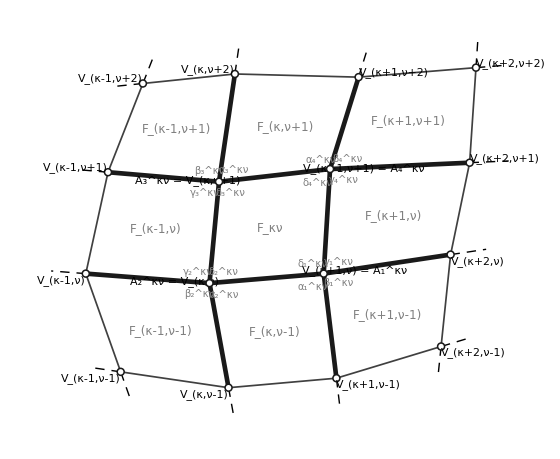
Given hypotheses:
The block with the central face F_κν has the vertices A_1^κν, A_2^κν, A_3^κν, A_4^κν with the quadruples of flat angles (α_1^κν, β_1^κν, γ_1^κν, δ_1^κν), (α_2^κν, β_2^κν, γ_2^κν, δ_2^κν), (α_3^κν, β_3^κν, γ_3^κν, δ_3^κν), (α_4^κν, β_4^κν, γ_4^κν, δ_4^κν), where
      (α_1^κν, β_1^κν, γ_1^κν, δ_1^κν) = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π).

Definitions:
The blocks F_κν and F_(κ,ν+1) share the vertices A_4^κν = A_1^(κ,ν+1) and A_3^κν = A_2^(κ,ν+1); the blocks F_κν and F_(κ+1,ν) share the vertices A_1^κν = A_2^(κ+1,ν) and A_4^κν = A_3^(κ+1,ν). Comparing the faces at these vertices:
(α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (δ_4^κν, γ_4^κν, β_4^κν, α_4^κν)
(α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ_3^κν, γ_3^κν, β_3^κν, α_3^κν)
(α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β_1^κν, α_1^κν, δ_1^κν, γ_1^κν)
(α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (β_4^κν, α_4^κν, δ_4^κν, γ_4^κν)
-Graphics-
The quadruples that a neighbouring block gets through the shared vertices by these four equations are called received; the quadruples that the relations of its own case (listed below) determine from a received one are called prescribed. The prescription of a whole net proceeds block by block from a given one, and it is well defined when every received quadruple coincides with the prescribed one.

Given cases (the relations of a block, superscripts omitted):
Case (a)  α_1==α_3==π-α_2==π-α_4,  β_1==β_3==π-β_2==π-β_4,  γ_1==γ_3==π-γ_2==π-γ_4,  δ_1==δ_3==π-δ_2==π-δ_4
Case (b)  α_1==β_4==π-α_2==π-β_3,  β_1==α_4==π-β_2==π-α_3,  γ_1==δ_4==π-γ_2==π-δ_3,  δ_1==γ_4==π-δ_2==π-γ_3
Case (c)  α_1==α_4==π-α_2==π-α_3,  β_1==β_4==π-β_2==π-β_3,  γ_1==γ_3==π-γ_2==π-γ_4,  δ_1==δ_3==π-δ_2==π-δ_4
Case (d)  α_1==β_4==π-α_2==π-β_3,  β_1==α_4==π-β_2==π-α_3,  γ_1==δ_3==π-γ_2==π-δ_4,  δ_1==γ_3==π-δ_2==π-γ_4
Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed.

We want to test the following claims ★ :
◼ Claim 1. In each case, the received quadruple (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) of the block F_(κ,ν+1) equals the prescribed one, the complement to π of the received (α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)).
◼ Claim 2. In each case, the received quadruple (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) of the block F_(κ+1,ν) equals the prescribed one, determined by the relations of the block from the received (α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)).
◼ Claim 3. In each case, the quadruple (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) of the block F_(κ+1,ν+1) received through F_(κ+1,ν) equals the one received through F_(κ,ν+1). Hence every block receives the same quadruples from all its neighbours, and the prescription of a net is well defined.

Claim 1: the block F_(κ,ν+1)Verified
Verification: the received quadruples are the reversed quadruples of the vertices 4 and 3 of the given block, taken from the solution of the relations of its case; the prescribed quadruple at the vertex 2 is the complement of the received quadruple at the vertex 1; each entry of the prescribed quadruple is compared with the corresponding entry of the received one, as a linear identity in α, β, γ, δ.
Case (a) :
    received: (α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (π-δ, π-γ, π-β, π-α)
    received: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ, γ, β, α)
    prescribed: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ, γ, β, α)

    to check, entry by entry:
        prescribed (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = received (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1))
    δ==δ ☑
    γ==γ ☑
    β==β ☑
    α==α ☑

Case (b) :
    received: (α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (γ, δ, α, β)
    received: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (π-γ, π-δ, π-α, π-β)
    prescribed: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (π-γ, π-δ, π-α, π-β)

    to check, entry by entry:
        prescribed (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = received (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1))
    π-γ==π-γ ☑
    π-δ==π-δ ☑
    π-α==π-α ☑
    π-β==π-β ☑

Case (c) :
    received: (α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (π-δ, π-γ, β, α)
    received: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ, γ, π-β, π-α)
    prescribed: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ, γ, π-β, π-α)

    to check, entry by entry:
        prescribed (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = received (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1))
    δ==δ ☑
    γ==γ ☑
    π-β==π-β ☑
    π-α==π-α ☑

Case (d) :
    received: (α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (π-γ, π-δ, α, β)
    received: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (γ, δ, π-α, π-β)
    prescribed: (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (γ, δ, π-α, π-β)

    to check, entry by entry:
        prescribed (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = received (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1))
    γ==γ ☑
    δ==δ ☑
    π-α==π-α ☑
    π-β==π-β ☑
Together, these give Claim 1.

Claim 2: the block F_(κ+1,ν)Verified
Verification: the received quadruples are the swapped quadruples of the vertices 1 and 4 of the given block; the block is prescribed from its vertex 1, the complement of the received vertex 2, by the relations of its own case, and its prescribed vertex 3 is compared with the received one entry by entry, as linear identities in α, β, γ, δ.
Case (a) :
    received: (α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β, α, δ, γ)
    received: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (π-β, π-α, π-δ, π-γ)
    prescribed: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (π-β, π-α, π-δ, π-γ)

    to check, entry by entry:
        prescribed (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = received (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν))
    π-β==π-β ☑
    π-α==π-α ☑
    π-δ==π-δ ☑
    π-γ==π-γ ☑

Case (b) :
    received: (α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β, α, δ, γ)
    received: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (α, β, γ, δ)
    prescribed: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (α, β, γ, δ)

    to check, entry by entry:
        prescribed (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = received (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν))
    α==α ☑
    β==β ☑
    γ==γ ☑
    δ==δ ☑

Case (c) :
    received: (α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β, α, δ, γ)
    received: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (β, α, π-δ, π-γ)
    prescribed: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (β, α, π-δ, π-γ)

    to check, entry by entry:
        prescribed (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = received (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν))
    β==β ☑
    α==α ☑
    π-δ==π-δ ☑
    π-γ==π-γ ☑

Case (d) :
    received: (α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β, α, δ, γ)
    received: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (α, β, π-γ, π-δ)
    prescribed: (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (α, β, π-γ, π-δ)

    to check, entry by entry:
        prescribed (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = received (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν))
    α==α ☑
    β==β ☑
    π-γ==π-γ ☑
    π-δ==π-δ ☑
Together, these give Claim 2.

Claim 3: the block F_(κ+1,ν+1)Verified
Verification: through the block to the right, that block is prescribed from its vertex 1 by the relations of its case and its vertex 4 is read reversed by the block above it; through the block above, that block reads the vertex 4 of the given block reversed, and the block to its right reads the swapped quadruple and takes its complement; the two received quadruples are compared entry by entry, as linear identities in α, β, γ, δ.
Case (a) :
    received through F_(κ+1,ν): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (γ, δ, α, β)
    received through F_(κ,ν+1): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (γ, δ, α, β)

    to check, entry by entry:
        (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ+1,ν) = (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ,ν+1)
    γ==γ ☑
    δ==δ ☑
    α==α ☑
    β==β ☑

Case (b) :
    received through F_(κ+1,ν): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (π-δ, π-γ, π-β, π-α)
    received through F_(κ,ν+1): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (π-δ, π-γ, π-β, π-α)

    to check, entry by entry:
        (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ+1,ν) = (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ,ν+1)
    π-δ==π-δ ☑
    π-γ==π-γ ☑
    π-β==π-β ☑
    π-α==π-α ☑

Case (c) :
    received through F_(κ+1,ν): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (γ, δ, π-α, π-β)
    received through F_(κ,ν+1): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (γ, δ, π-α, π-β)

    to check, entry by entry:
        (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ+1,ν) = (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ,ν+1)
    γ==γ ☑
    δ==δ ☑
    π-α==π-α ☑
    π-β==π-β ☑

Case (d) :
    received through F_(κ+1,ν): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (δ, γ, π-β, π-α)
    received through F_(κ,ν+1): (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) = (δ, γ, π-β, π-α)

    to check, entry by entry:
        (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ+1,ν) = (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through F_(κ,ν+1)
    δ==δ ☑
    γ==γ ☑
    π-β==π-β ☑
    π-α==π-α ☑
Together, these give Claim 3.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,X,statusChip,smallChip,colTest,bullet,colRec,colPre,recW,preW,cases,caseCol,unk,relsOf,relDisp,quadOf,vertsOf,revOf,swapOf,complOf,above,right,quadDisp,vDisp,lstS,eqLine,vtx,face,sKN,sKN1,sK1N,sK1N1,resultsAll,figBlock];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colTest=RGBColor[0.10,0.35,0.75];bullet=Style["◼ ",12,colTest];
colRec=RGBColor[0.80,0.35,0.05];colPre=RGBColor[0.00,0.50,0.30];
recW=Style["received",Bold,colRec];preW=Style["prescribed",Bold,colPre];
(*The block with the central face F[kappa,nu] has the vertices A[kappa nu]_1,...,A[kappa nu]_4 and the flat angles alpha[kappa nu]_i,beta[kappa nu]_i,gamma[kappa nu]_i,delta[kappa nu]_i,i=1,2,3,4. The flat angles at the vertex 1 are the independent symbols alpha,beta,gamma,delta;those at the vertices 2,3,4 are the unique solution of the relations of each case,found by Solve.The blocks (kappa,nu+1) and (kappa+1,nu) receive four of their quadruples from the block (kappa,nu) through the shared vertices and prescribe the rest by the relations of their own case.Every check below is a linear identity in alpha,beta,gamma,delta,decided by Simplify.*)
X={α,β,γ,δ};
cases={"(a)","(b)","(c)","(d)"};
caseCol["(a)"]=RGBColor[0.55,0.33,0.10];caseCol["(b)"]=RGBColor[0.00,0.45,0.25];caseCol["(c)"]=RGBColor[0.10,0.45,0.65];caseCol["(d)"]=RGBColor[0.55,0.15,0.25];
unk={{a2,b2,g2,d2},{a3,b3,g3,d3},{a4,b4,g4,d4}};
relsOf["(a)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[3]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[4]]),b[[1]]-b[[3]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[4]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(b)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[4]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[3]]),d[[1]]-g[[4]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[3]])}];
relsOf["(c)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[3]]),b[[1]]-b[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[3]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(d)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[4]]),d[[1]]-g[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[4]])}];
relDisp["(a)"]={HoldForm[Subscript[α,1]==Subscript[α,3]==π-Subscript[α,2]==π-Subscript[α,4]],HoldForm[Subscript[β,1]==Subscript[β,3]==π-Subscript[β,2]==π-Subscript[β,4]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(b)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,4]==π-Subscript[γ,2]==π-Subscript[δ,3]],HoldForm[Subscript[δ,1]==Subscript[γ,4]==π-Subscript[δ,2]==π-Subscript[γ,3]]};
relDisp["(c)"]={HoldForm[Subscript[α,1]==Subscript[α,4]==π-Subscript[α,2]==π-Subscript[α,3]],HoldForm[Subscript[β,1]==Subscript[β,4]==π-Subscript[β,2]==π-Subscript[β,3]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(d)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,3]==π-Subscript[γ,2]==π-Subscript[δ,4]],HoldForm[Subscript[δ,1]==Subscript[γ,3]==π-Subscript[δ,2]==π-Subscript[γ,4]]};
(*the four quadruples (vertices 1,2,3,4) of the block of case c whose vertex 1 carries the quadruple Y*)
quadOf[c_,Y_List]:=Module[{sol=Solve[Thread[relsOf[c][Prepend[unk,Y]]==0],Flatten[unk]]},If[Length[sol]==1,Prepend[unk/. sol[[1]],Y],Missing[]]];
Do[vertsOf[c]=quadOf[c,X],{c,cases}];
(*the transfers through a shared vertex:the reversal for two blocks one above the other,the swap within the pairs for two blocks side by side;the complement to pi*)
revOf[{a_,b_,g_,d_}]:={d,g,b,a};swapOf[{a_,b_,g_,d_}]:={b,a,d,g};complOf[Y_List]:=π-Y;
above[V_]:={revOf[V[[4]]],revOf[V[[3]]]};        (*received by the block (kappa,nu+1) at its vertices 1 and 2*)
right[V_]:={swapOf[V[[1]]],swapOf[V[[4]]]};      (*received by the block (kappa+1,nu) at its vertices 2 and 3*)
(*displays*)
sKN=Row[{κ,ν}];sKN1=Row[{κ,",",ν,"+1"}];sK1N=Row[{κ,"+1,",ν}];sK1N1=Row[{κ,"+1,",ν,"+1"}];
lstS[i_,sup_]:={Subsuperscript[α,i,sup],Subsuperscript[β,i,sup],Subsuperscript[γ,i,sup],Subsuperscript[δ,i,sup]};
quadDisp[Y_List]:=TraditionalForm[Row[{"(",Row[Riffle[Y,", "]],")"}]];
vDisp[i_,sup_]:=quadDisp[lstS[i,sup]];
vtx[i_,sup_]:=TraditionalForm[Subsuperscript[A,i,sup]];
face[sup_]:=TraditionalForm[Subscript[F,sup]];
eqLine[lhs_,rhs_]:=Row[{lhs," = ",rhs}];
resultsAll={};
(*the figure of the block,drawn by the notebook:an irregular 3 x 3 block,its nine faces,the vertices,the flat angles in the faces containing them,and dashed stubs for the rest of the net*)
figBlock=Module[{W,thin,thick,cont,dot,ang,lab,fl,faceCenter,angleAt,vName,sup,seg,grey=GrayLevel[0.5],bg=RGBColor[0.99,0.96,0.88]},W[0,0]={0.3,0.0};W[1,0]={3.7,-0.5};W[2,0]={7.1,-0.2};W[3,0]={10.4,0.8};
W[0,1]={-0.8,3.1};W[1,1]={3.1,2.8};W[2,1]={6.7,3.1};W[3,1]={10.7,3.7};
W[0,2]={-0.1,6.3};W[1,2]={3.4,6.0};W[2,2]={6.9,6.4};W[3,2]={11.3,6.6};
W[0,3]={1.0,9.1};W[1,3]={3.9,9.4};W[2,3]={7.8,9.3};W[3,3]={11.5,9.6};
faceCenter[i_,j_]:=(W[i,j]+W[i+1,j+1]+W[i+1,j]+W[i,j+1])/4;
sup[k_,n_]:=Row[{Which[k==-1,Row[{κ,"-1"}],k==0,κ,k==1,Row[{κ,"+1"}]],If[k==0&&n==0,"",","],Which[n==-1,Row[{ν,"-1"}],n==0,ν,n==1,Row[{ν,"+1"}]]}];
vName[i_,j_]:=Style[TraditionalForm[Subscript[V,Row[{Which[i==0,Row[{κ,"-1"}],i==1,κ,i==2,Row[{κ,"+1"}],i==3,Row[{κ,"+2"}]],",",Which[j==0,Row[{ν,"-1"}],j==1,ν,j==2,Row[{ν,"+1"}],j==3,Row[{ν,"+2"}]]}]]],11];
seg[p_,q_,t_]:=p+t (q-p);
thin={Thickness[0.0022],GrayLevel[0.25],Line[{W[0,0],W[1,0],W[2,0],W[3,0],W[3,1],W[3,2],W[3,3],W[2,3],W[1,3],W[0,3],W[0,2],W[0,1],W[0,0]}]};
thick={Thickness[0.006],GrayLevel[0.1],Line[{W[1,1],W[2,1],W[2,2],W[1,2],W[1,1]}],Line[{W[1,1],W[1,0]}],Line[{W[1,1],W[0,1]}],Line[{W[2,1],W[2,0]}],Line[{W[2,1],W[3,1]}],Line[{W[1,2],W[1,3]}],Line[{W[1,2],W[0,2]}],Line[{W[2,2],W[2,3]}],Line[{W[2,2],W[3,2]}]};
cont={Thickness[0.0018],Black,Dashing[{0.012,0.009}],Sequence@@Table[Line[{W[i,0],seg[W[i,0],W[i,1],-0.28]}],{i,0,3}],Sequence@@Table[Line[{W[i,3],seg[W[i,3],W[i,2],-0.28]}],{i,0,3}],Sequence@@Table[Line[{W[0,j],seg[W[0,j],W[1,j],-0.28]}],{j,0,3}],Sequence@@Table[Line[{W[3,j],seg[W[3,j],W[2,j],-0.28]}],{j,0,3}]};
dot={White,EdgeForm[{GrayLevel[0.1],Thickness[0.002]}],Sequence@@Table[Disk[W[i,j],0.11],{i,0,3},{j,0,3}]};
fl=Table[Text[Style[TraditionalForm[Subscript[F,sup[i-1,j-1]]],12,grey],faceCenter[i,j]],{i,0,2},{j,0,2}];
angleAt[i_,j_,ci_,cj_,letter_,k_]:=Text[Style[TraditionalForm[Subsuperscript[letter,k,sKN]],10,grey],seg[W[i,j],faceCenter[ci,cj],0.22]];
ang={angleAt[2,1,1,1,δ,1],angleAt[2,1,1,0,α,1],angleAt[2,1,2,1,γ,1],angleAt[2,1,2,0,β,1],angleAt[1,1,1,1,δ,2],angleAt[1,1,1,0,α,2],angleAt[1,1,0,1,γ,2],angleAt[1,1,0,0,β,2],angleAt[1,2,1,1,δ,3],angleAt[1,2,1,2,α,3],angleAt[1,2,0,1,γ,3],angleAt[1,2,0,2,β,3],angleAt[2,2,1,1,δ,4],angleAt[2,2,1,2,α,4],angleAt[2,2,2,1,γ,4],angleAt[2,2,2,2,β,4]};
lab={Text[Framed[Style[eqLine[vName[2,1],vtx[1,sKN]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[2,1],W[3,1],0.24],{-1,0}],Text[Framed[Style[eqLine[vtx[2,sKN],vName[1,1]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[1,1],W[0,1],0.28],{1,0}],Text[Framed[Style[eqLine[vtx[3,sKN],vName[1,2]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[1,2],W[0,2],0.28],{1,0}],Text[Framed[Style[eqLine[vName[2,2],vtx[4,sKN]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[2,2],W[3,2],0.24],{-1,0}],Text[vName[0,0],W[0,0],{1.3,1.1}],Text[vName[1,0],W[1,0],{1.1,1.1}],Text[vName[2,0],W[2,0],{-1.6,1.1}],Text[vName[3,0],W[3,0],{-1.4,1.1}],Text[vName[0,1],W[0,1],{1.3,1.1}],Text[vName[3,1],W[3,1],{-1.4,1.1}],Text[vName[0,2],W[0,2],{1.3,-1.1}],Text[vName[3,2],W[3,2],{-1.4,-1.1}],Text[vName[0,3],W[0,3],{1.3,-1.1}],Text[vName[1,3],W[1,3],{1.1,-1.1}],Text[vName[2,3],W[2,3],{-1.6,-1.1}],Text[vName[3,3],W[3,3],{-1.4,-1.1}]};
Graphics[{cont,thin,thick,fl,ang,dot,lab},ImageSize->560,PlotRangePadding->1.2,Background->None,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"The block with the central face ",face[sKN]," has the vertices ",vtx[1,sKN],", ",vtx[2,sKN],", ",vtx[3,sKN],", ",vtx[4,sKN]," with the quadruples of flat angles ",vDisp[1,sKN],", ",vDisp[2,sKN],", ",vDisp[3,sKN],", ",vDisp[4,sKN],", where"}],13],Style[Row[{"      ",eqLine[vDisp[1,sKN],quadDisp[X]],",   α, β, γ, δ ∈ (0, π)."}],13],"",Style["Definitions:",Bold,14],Style[Row[{"The blocks ",face[sKN]," and ",face[sKN1]," share the vertices ",eqLine[vtx[4,sKN],vtx[1,sKN1]]," and ",eqLine[vtx[3,sKN],vtx[2,sKN1]],"; the blocks ",face[sKN]," and ",face[sK1N]," share the vertices ",eqLine[vtx[1,sKN],vtx[2,sK1N]]," and ",eqLine[vtx[4,sKN],vtx[3,sK1N]],". Comparing the faces at these vertices:"}],13],Style[Column[{eqLine[vDisp[1,sKN1],quadDisp[revOf[lstS[4,sKN]]]],eqLine[vDisp[2,sKN1],quadDisp[revOf[lstS[3,sKN]]]],eqLine[vDisp[2,sK1N],quadDisp[swapOf[lstS[1,sKN]]]],eqLine[vDisp[3,sK1N],quadDisp[swapOf[lstS[4,sKN]]]]},Alignment->Left,Spacings->0.6],13],figBlock,Style[Row[{"The quadruples that a neighbouring block gets through the shared vertices by these four equations are called ",recW,"; the quadruples that the relations of its own case (listed below) determine from a received one are called ",preW,". The prescription of a whole net proceeds block by block from a given one, and it is well defined when every received quadruple coincides with the prescribed one."}],13],"",Style["Given cases (the relations of a block, superscripts omitted):",Bold,14],Sequence@@Table[Style[Row[{Style["Case "<>c<>"  ",Bold,13],Row[Riffle[TraditionalForm/@relDisp[c],",  "]]}],13,caseCol[c]],{c,cases}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style[Row[{"Claim 1. In each case, the received quadruple ",vDisp[2,sKN1]," of the block ",face[sKN1]," equals the prescribed one, the complement to π of the received ",vDisp[1,sKN1],"."}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"Claim 2. In each case, the received quadruple ",vDisp[3,sK1N]," of the block ",face[sK1N]," equals the prescribed one, determined by the relations of the block from the received ",vDisp[2,sK1N],"."}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"Claim 3. In each case, the quadruple ",vDisp[1,sK1N1]," of the block ",face[sK1N1]," received through ",face[sK1N]," equals the one received through ",face[sKN1],". Hence every block receives the same quadruples from all its neighbours, and the prescription of a net is well defined."}],Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=RGBColor[0.10,0.35,0.75],rows={},ok=True,ind="    "},Do[Module[{V=vertsOf[c],rec,oks,lines},rec=above[V];
oks=Table[Simplify[rec[[2,j]]-(π-rec[[1,j]])]===0,{j,4}];
lines=Table[With[{l=π-rec[[1,j]],r=rec[[2,j]]},Row[{TraditionalForm[HoldForm[l==r]]," ",smallChip[oks[[j]]]}]],{j,4}];
ok=ok&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Style[Column[{Row[{ind,recW,": ",eqLine[vDisp[1,sKN1],quadDisp[rec[[1]]]]}],Row[{ind,recW,": ",eqLine[vDisp[2,sKN1],quadDisp[rec[[2]]]]}],Row[{ind,preW,": ",eqLine[vDisp[2,sKN1],quadDisp[π-rec[[1]]]]}],"",Row[{ind,"to check, entry by entry:"}],Row[{ind,ind,preW," ",vDisp[2,sKN1]," = ",recW," ",vDisp[2,sKN1]}]},Spacings->0.4],13],Column[Table[Style[Row[{ind,ln}],13],{ln,lines}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style[Row[{"Claim 1: the block ",face[sKN1]}],Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification: the received quadruples are the reversed quadruples of the vertices 4 and 3 of the given block, taken from the solution of the relations of its case; the prescribed quadruple at the vertex 2 is the complement of the received quadruple at the vertex 1; each entry of the prescribed quadruple is compared with the corresponding entry of the received one, as a linear identity in α, β, γ, δ.",Bold,13]},Most[rows],{Style["Together, these give Claim 1.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=RGBColor[0.50,0.20,0.65],rows={},ok=True,ind="    "},Do[Module[{V=vertsOf[c],rec,own,oks,lines},rec=right[V];
own=quadOf[c,complOf[rec[[1]]]];
oks=Table[Simplify[own[[3,j]]-rec[[2,j]]]===0,{j,4}];
lines=Table[With[{l=own[[3,j]],r=rec[[2,j]]},Row[{TraditionalForm[HoldForm[l==r]]," ",smallChip[oks[[j]]]}]],{j,4}];
ok=ok&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Style[Column[{Row[{ind,recW,": ",eqLine[vDisp[2,sK1N],quadDisp[rec[[1]]]]}],Row[{ind,recW,": ",eqLine[vDisp[3,sK1N],quadDisp[rec[[2]]]]}],Row[{ind,preW,": ",eqLine[vDisp[3,sK1N],quadDisp[own[[3]]]]}],"",Row[{ind,"to check, entry by entry:"}],Row[{ind,ind,preW," ",vDisp[3,sK1N]," = ",recW," ",vDisp[3,sK1N]}]},Spacings->0.4],13],Column[Table[Style[Row[{ind,ln}],13],{ln,lines}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style[Row[{"Claim 2: the block ",face[sK1N]}],Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification: the received quadruples are the swapped quadruples of the vertices 1 and 4 of the given block; the block is prescribed from its vertex 1, the complement of the received vertex 2, by the relations of its own case, and its prescribed vertex 3 is compared with the received one entry by entry, as linear identities in α, β, γ, δ.",Bold,13]},Most[rows],{Style["Together, these give Claim 2.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=RGBColor[0.00,0.55,0.55],rows={},ok=True,ind="    "},Do[Module[{V=vertsOf[c],viaRight,viaAbove,oks,lines},viaRight=revOf[quadOf[c,complOf[right[V][[1]]]][[4]]];
viaAbove=complOf[swapOf[above[V][[1]]]];
oks=Table[Simplify[viaRight[[j]]-viaAbove[[j]]]===0,{j,4}];
lines=Table[With[{l=viaRight[[j]],r=viaAbove[[j]]},Row[{TraditionalForm[HoldForm[l==r]]," ",smallChip[oks[[j]]]}]],{j,4}];
ok=ok&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Style[Column[{Row[{ind,recW," through ",face[sK1N],": ",eqLine[vDisp[1,sK1N1],quadDisp[viaRight]]}],Row[{ind,recW," through ",face[sKN1],": ",eqLine[vDisp[1,sK1N1],quadDisp[viaAbove]]}],"",Row[{ind,"to check, entry by entry:"}],Row[{ind,ind,vDisp[1,sK1N1]," through ",face[sK1N]," = ",vDisp[1,sK1N1]," through ",face[sKN1]}]},Spacings->0.4],13],Column[Table[Style[Row[{ind,ln}],13],{ln,lines}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style[Row[{"Claim 3: the block ",face[sK1N1]}],Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification: through the block to the right, that block is prescribed from its vertex 1 by the relations of its case and its vertex 4 is read reversed by the block above it; through the block above, that block reads the vertex 4 of the given block reversed, and the block to its right reads the swapped quadruple and takes its complement; the two received quadruples are compared entry by entry, as linear identities in α, β, γ, δ.",Bold,13]},Most[rows],{Style["Together, these give Claim 3.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```